```mathematica
ClearAll[a,b,E0,omega,k,mu,epsilon,c,kc2,Ez,Hz, gradEz,Et,Ht,e3, gradHz, Hz]

(*Parameters*)a=1;b=1; (*Waveguide dimensions*)
E0=1; (*Amplitude*)
omega=2 Pi; (*Angular frequency*)
k=Pi; (*Wave number*)
mu=1;epsilon=1; (*Medium properties*)
c=1/Sqrt[mu epsilon]; (*Speed of light*)
kc2=omega^2 mu epsilon-k^2; (*Cutoff wavenumber squared*)
e3 = {0,0,1};

(* (Scalar) Longitudinal electric and magnetic fields E_z, H_z *)
Ez[x_,y_,z_,t_]:=E0 Cos[Pi x/a] Cos[Pi y/b] Exp[I (omega t-k z)];
Hz[x_,y_,z_,t_] := 0;

(*Transverse gradient of E_z*)
gradEz[x_,y_,z_,t_]:={D[Ez[xx,y,z,t],xx],D[Ez[x,yy,z,t],yy], 0}/. {xx:> x, yy :> y};
gradHz[x_,y_,z_,t_]:={D[Hz[xx,y,z,t],xx],D[Hz[x,yy,z,t],yy], 0}/. {xx:> x, yy :> y};

(*Transverse electric field E_t*)
Et[x_,y_,z_,t_]:=(I /kc2) (k gradEz[x,y,z,t] + mu omega Cross[e3, gradHz[x,y,z,t]]);

(*Transverse magnetic field H_t*)
Ht[x_,y_,z_,t_]:=-(I /kc2) (
epsilon omega Cross[e3,gradEz[x,y,z,t]]
+ k gradHz[x,y,z,t]
);

(*gradEz[xx, yy, zz, tt]//MatrixForm
Et[xx,yy,zz, tt]//MatrixForm
Ht[xx,yy,zz, tt]//MatrixForm
Ez[xx,yy,zz, tt]
Hz[xx,yy,zz, tt]*)

ClearAll[Efield,Hfield,t0, EtReal,HtReal,EzReal]

(*Full electric and magnetic fields*)
Efield[x_,y_,z_,t_]:= Et[x,y,z,t] + e3 Ez[x,y,z,t];
Hfield[x_,y_,z_,t_]:= Ht[x,y,z,t] + e3 Hz[x,y,z,t];

(*Real parts for plotting,at t=0*)
t0=0;
EtReal[x_,y_,z_]:=Re[Et[x,y,z,t0]];
HtReal[x_,y_,z_]:=Re[Ht[x,y,z,t0]];
EzReal[x_,y_,z_]:=Re[Ez[x,y,z,t0]];
```

```mathematica
Animate[
VectorPlot3D[Re[ Efield[x,y,z, t]],{x,0,a},{y,0,b},{z,0,2},VectorPoints->{8,8,8},VectorScale->{Small,Scaled[0.5]},VectorStyle->Red,VectorColorFunction->None,PlotLabel->"Total Electric Field"],
{t, 0, 3}
];
```

```mathematica
Animate[
VectorPlot3D[Re[ Et[x,y,z, t]],{x,0,a},{y,0,b},{z,0,2},VectorPoints->{8,8,8},VectorScale->{Small,Scaled[0.5]},VectorStyle->Red,VectorColorFunction->None,PlotLabel->"Transverse Electric Field"],
{t, 0, 3}
];
```

```mathematica
Animate[
VectorPlot3D[Re[ Hfield[x,y,z, t]],{x,0,a},{y,0,b},{z,0,2},VectorPoints->{8,8,8},VectorScale->{Small,Scaled[0.5]},VectorStyle->Red,VectorColorFunction->None,PlotLabel->"Total Magnetic Field"],
{t, 0, 3}
];
```

```mathematica
Animate[
VectorPlot3D[Re[ Ht[x,y,z, t]],{x,0,a},{y,0,b},{z,0,2},VectorPoints->{8,8,8},VectorScale->{Small,Scaled[0.5]},VectorStyle->Red,VectorColorFunction->None,PlotLabel->"Transverse Magnetic Field"],
{t, 0, 3}
];
```

-Graphics3D-

-Graphics3D-

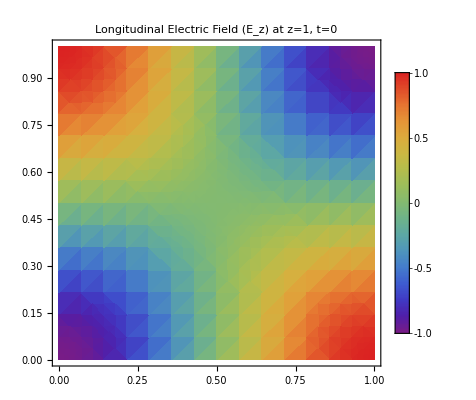

-Graphics3D-

```mathematica
ClearAll[eField,hField,ezField]

(*Vector field plot for E_t*)
eField=VectorPlot3D[EtReal[x,y,z],{x,0,a},{y,0,b},{z,0,2},VectorPoints->{8,8,8},VectorScale->{Small,Scaled[0.5]},VectorStyle->Red,VectorColorFunction->None,PlotLabel->"Transverse Electric Field (E_t) at t=0"]

(*Vector field plot for H_t*)
hField=VectorPlot3D[HtReal[x,y,z],{x,0,a},{y,0,b},{z,0,2},VectorPoints->{8,8,8},VectorScale->{Small,Scaled[0.5]},VectorStyle->Blue,VectorColorFunction->None,PlotLabel->"Transverse Magnetic Field (H_t) at t=0"]

(*Scalar field plot for E_z as a density plot on z=1 plane*)
ezField=DensityPlot[EzReal[x,y,1],{x,0,a},{y,0,b},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotLabel->"Longitudinal Electric Field (E_z) at z=1, t=0"]

(*Table[EtReal[x,y,z],{x,0,a, 0.5},{y,0,b, 0.5},{z,0,2, 0.5}]// N*)

(*Combine plots*)
TransverseFieldFig1 = Show[eField,hField,Graphics3D[{Opacity[0.5],GeometricTransformation[First@Plot3D[0,{x,0,a},{y,0,b},Mesh->None,ColorFunction->Function[{x,y},ColorData["Rainbow"][EzReal[x,y,1]]]],TranslationTransform[{0,0,1}]]}],PlotRange->{{0,a},{0,b},{0,2}},Axes->True,AxesLabel->{"x","y","z"},BoxRatios->{1,1,2}]
```

```mathematica
ClearAll[divE,divH,curlE,curlH,jomegaMuH,jomegaEpsilonE,samplePoint,divEVal,divHVal,curlEVal,jomegaMuHVal,curlHVal,jomegaEpsilonEVal]

(*Maxwell's Equations Check*)
(*Divergence of E*)
divE[x_,y_,z_,t_]:=Div[Efield[x,y,z,t],{x,y,z}];

(*Divergence of H*)
divH[x_,y_,z_,t_]:=Div[Hfield[x,y,z,t],{x,y,z}];

(*Curl of E*)
curlE[x_,y_,z_,t_]:=Curl[Efield[x,y,z,t],{x,y,z}];

(*Curl of H*)
curlH[x_,y_,z_,t_]:=Curl[Hfield[x,y,z,t],{x,y,z}];

(*Time derivative terms*)
jomegaMuH[x_,y_,z_,t_]:=-I omega mu Hfield[x,y,z,t];
jomegaEpsilonE[x_,y_,z_,t_]:=I omega epsilon Efield[x,y,z,t];

(*Check Maxwell's equations at a sample point*)
samplePoint={0.5,0.5,1,0};
{divEVal,divHVal,curlEVal,jomegaMuHVal,curlHVal,jomegaEpsilonEVal}={divE[x,y,z,t],divH[x,y,z,t],curlE[x,y,z,t],jomegaMuH[x,y,z,t],curlH[x,y,z,t],jomegaEpsilonE[x,y,z,t]}/. {x->0.5,y->0.5,z->1,t->0};

(*Simplify and compare*)
Print["Divergence of E: ",Simplify[divEVal]];
Print["Divergence of H: ",Simplify[divHVal]];
Print["Curl of E vs -j omega mu H: ",Simplify[curlEVal-jomegaMuHVal]];
Print["Curl of H vs j omega epsilon E: ",Simplify[curlHVal-jomegaEpsilonEVal]];
```

Divergence of E: 0.+1.96318×10^-32 ⅈ

Divergence of H: 0

Curl of E vs -j omega mu H: {-1.28245×10^-16,1.28245×10^-16,0}

Curl of H vs j omega epsilon E: {2.56489×10^-16,2.56489×10^-16,0.+7.85272×10^-33 ⅈ}